# AntonAntonov/SSparseMatrix

Sparse matrices with named columns and rows

## Paclet Manifest

"Documentation"

"English"

"Guides"

"SSparseMatrixobjects.nb"DocumentationEnglishGuidesSSparseMatrixobjects.nb

"ReferencePages"

"Symbols"

"ColumnAssociations.nb"DocumentationEnglishReferencePagesSymbolsColumnAssociations.nb

"ColumnBind.nb"DocumentationEnglishReferencePagesSymbolsColumnBind.nb

"ColumnMaxesAssociation.nb"DocumentationEnglishReferencePagesSymbolsColumnMaxesAssociation.nb

"ColumnMaxes.nb"DocumentationEnglishReferencePagesSymbolsColumnMaxes.nb

"ColumnMinsAssociation.nb"DocumentationEnglishReferencePagesSymbolsColumnMinsAssociation.nb

"ColumnMins.nb"DocumentationEnglishReferencePagesSymbolsColumnMins.nb

"ColumnNamesAssociation.nb"DocumentationEnglishReferencePagesSymbolsColumnNamesAssociation.nb

"ColumnNames.nb"DocumentationEnglishReferencePagesSymbolsColumnNames.nb

"ColumnsCount.nb"DocumentationEnglishReferencePagesSymbolsColumnsCount.nb

"ColumnSumsAssociation.nb"DocumentationEnglishReferencePagesSymbolsColumnSumsAssociation.nb

"ColumnSums.nb"DocumentationEnglishReferencePagesSymbolsColumnSums.nb

"DimensionNamesAssociation.nb"DocumentationEnglishReferencePagesSymbolsDimensionNamesAssociation.nb

"DimensionNames.nb"DocumentationEnglishReferencePagesSymbolsDimensionNames.nb

"ImposeColumnNames.nb"DocumentationEnglishReferencePagesSymbolsImposeColumnNames.nb

"ImposeRowNames.nb"DocumentationEnglishReferencePagesSymbolsImposeRowNames.nb

"MakeSSparseMatrix.nb"DocumentationEnglishReferencePagesSymbolsMakeSSparseMatrix.nb

"RowAssociations.nb"DocumentationEnglishReferencePagesSymbolsRowAssociations.nb

"RowBind.nb"DocumentationEnglishReferencePagesSymbolsRowBind.nb

"RowMaxesAssociation.nb"DocumentationEnglishReferencePagesSymbolsRowMaxesAssociation.nb

"RowMaxes.nb"DocumentationEnglishReferencePagesSymbolsRowMaxes.nb

"RowMinsAssociation.nb"DocumentationEnglishReferencePagesSymbolsRowMinsAssociation.nb

"RowMins.nb"DocumentationEnglishReferencePagesSymbolsRowMins.nb

"RowNamesAssociation.nb"DocumentationEnglishReferencePagesSymbolsRowNamesAssociation.nb

"RowNames.nb"DocumentationEnglishReferencePagesSymbolsRowNames.nb

"RowsCount.nb"DocumentationEnglishReferencePagesSymbolsRowsCount.nb

"RowSumsAssociation.nb"DocumentationEnglishReferencePagesSymbolsRowSumsAssociation.nb

"RowSums.nb"DocumentationEnglishReferencePagesSymbolsRowSums.nb

"SetColumnNames.nb"DocumentationEnglishReferencePagesSymbolsSetColumnNames.nb

"SetDimensionNames.nb"DocumentationEnglishReferencePagesSymbolsSetDimensionNames.nb

"SetRowNames.nb"DocumentationEnglishReferencePagesSymbolsSetRowNames.nb

"SSparseMatrixAssociation.nb"DocumentationEnglishReferencePagesSymbolsSSparseMatrixAssociation.nb

"SSparseMatrixImportFromDirectory.nb"DocumentationEnglishReferencePagesSymbolsSSparseMatrixImportFromDirectory.nb

"SSparseMatrix.nb"DocumentationEnglishReferencePagesSymbolsSSparseMatrix.nb

"SSparseMatrixQ.nb"DocumentationEnglishReferencePagesSymbolsSSparseMatrixQ.nb

"SSparseMatrixToTriplets.nb"DocumentationEnglishReferencePagesSymbolsSSparseMatrixToTriplets.nb

"ToSSparseMatrix.nb"DocumentationEnglishReferencePagesSymbolsToSSparseMatrix.nb

"Tutorials"

"Kernel"

"SSparseMatrix.wl"KernelSSparseMatrix.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

The paclet provides objects that are sparse matrices with named columns and rows (based on SparseArray.)

### Details

Sub-matrix extraction by column- and row names.

Column- and row names propagation for dot products.

Column- and row binding of sparse matrices.

Column- and row  sums.

Tabulation and visualization (of sparse matrices with named rows and columns.)

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`SSparseMatrix`"];
```

### Basic Examples

Here we create a SSparseMatrix object:

```mathematica
smat=ToSSparseMatrix[
{{1,1}->1,{2,2}->2,{4,3}->3,{1,4}->4,{3,5}->2},
"ColumnNames"->{"a","b","c","d","e"},
"RowNames"->{"A","B","C","D"},
"DimensionNames"->{"U","V"}]
```

SparseArray[…]

The function MatrixForm shows the SSparseMatrix objects with their row and column names:

```mathematica
smat//MatrixForm
```

( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0)

Here we apply MatrixPlot:

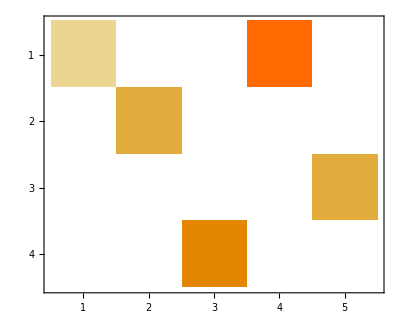

```mathematica
smat//MatrixPlot
```

### Scope

#### Query functions

These functions can be used to retrieve the names of rows, columns, and dimensions:

```mathematica
RowNames[smat]
```

{A,B,C,D}

```mathematica
ColumnNames[smat]
```

{a,b,c,d,e}

```mathematica
DimensionNames[smat]
```

{U,V}

(They correspond to S's and R's functions rownames, colnames, dimnames.)

Underlying sparse array:

```mathematica
SparseArray[smat]
```

SparseArray[…]

Dimensions:

```mathematica
Dimensions[smat]
```

{4,5}

Array rules:

```mathematica
ArrayRules[smat]
```

{{1,1}→1,{1,4}→4,{2,2}→2,{3,5}→2,{4,3}→3,{_,_}→0}

#### Set row names

Here is a copy of the sparse matrix:

```mathematica
smat2=smat;
MatrixForm[smat2]
```

( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0)

Here we set different row names:

```mathematica
smat2=SetRowNames[smat2,ToString/@Range[RowsCount[smat]]]
```

SparseArray[…]

Matrix form of the result:

```mathematica
MatrixForm[smat2]
```

( | a | b | c | d | e
1 | 1 | 0 | 0 | 4 | 0
2 | 0 | 2 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 2
4 | 0 | 0 | 3 | 0 | 0)

#### Set column names

Here we set different column names:

```mathematica
smat2=SetColumnNames[smat2,ToString/@Range[ColumnsCount[smat]]]
```

SparseArray[…]

Matrix form of the result:

```mathematica
MatrixForm[smat2]
```

( | 1 | 2 | 3 | 4 | 5
1 | 1 | 0 | 0 | 4 | 0
2 | 0 | 2 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 2
4 | 0 | 0 | 3 | 0 | 0)

#### Transpose

Here we transpose and show the matrix form:

```mathematica
Transpose[smat]//MatrixForm
```

( | A | B | C | D
a | 1 | 0 | 0 | 0
b | 0 | 2 | 0 | 0
c | 0 | 0 | 0 | 3
d | 4 | 0 | 0 | 0
e | 0 | 0 | 2 | 0)

#### Sums

Here is the sum of all elements:

```mathematica
Total[smat,2]
```

12

Here are the row sums:

```mathematica
RowSums[smat]
```

{5,2,2,3}

Here are the column sums:

```mathematica
ColumnSums[smat]
```

{1,2,3,4,2}

Here are the row sums as Association:

```mathematica
RowSumsAssociation[smat]
```

<|A→5,B→2,C→2,D→3|>

Here are the column sums as Association:

```mathematica
ColumnSumsAssociation[smat]
```

<|a→1,b→2,c→3,d→4,e→2|>

#### Dot products

In order to make the SSparseMatrix objects really useful we have to implement matrix-vector and matrix-matrix operations for them. (With other SSparseMatrix objects and with SparseArray objects.)

This function is used to visualize the commands, the results, and the results’ heads.

```mathematica
Clear[ResultsGrid]
ResultsGrid[expressions_Inactive,opts___]:=
Block[{t,t1},
t=Map[HoldForm,expressions,{2}];
t1=ReleaseHold[Activate[t]];
Grid[MapThread[Prepend,{{Activate[t],MatrixForm/@t1,Head/@t1},Style[#,Blue,FontFamily->"Times"]&/@{"expr","result","head"}}],opts]
];
```

#### Matrix by vector multiplication

```mathematica
ResultsGrid[Inactive[{smat,Transpose@smat⟦{1},All⟧,smat.Transpose@smat⟦{1},All⟧}],Dividers->All]
```

expr | smat | Transpose[smat⟦{1},All⟧] | smat.Transpose[smat⟦{1},All⟧]
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | ( | A
a | 1
b | 0
c | 0
d | 4
e | 0) | ( | A
A | 17
B | 0
C | 0
D | 0)
head | SSparseMatrix | SSparseMatrix | SSparseMatrix

```mathematica
ResultsGrid[Inactive[{smat,smat⟦1,All⟧,smat.smat⟦1,All⟧}],Dividers->All]
```

expr | smat | smat⟦1,All⟧ | smat.smat⟦1,All⟧
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | (1
0
0
4
0) | (A | 17
B | 0
C | 0
D | 0)
head | SSparseMatrix | SparseArray | SSparseMatrix

#### Matrix by matrix multiplication

Here is a sparse matrix (2D sparse array):

```mathematica
mat=SparseArray[{{1,1}->1,{2,2}->2,{1,4}->4,{3,5}->2,{4,3}->3}]
```

SparseArray[…]

First we look into a dot product to the right of SSparseMatrix with a sparse array and a dot product to the left of SSparseMatrix with a sparse array:

```mathematica
ResultsGrid[Inactive[{smat,mat,smat.Transpose[mat],Transpose[mat].smat}],Dividers->All]
```

expr | smat | mat | smat.Transpose[mat] | Transpose[mat].smat
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | (1 | 0 | 0 | 4 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2
0 | 0 | 3 | 0 | 0) | (A | 17 | 0 | 0 | 0
B | 0 | 4 | 0 | 0
C | 0 | 0 | 4 | 0
D | 0 | 0 | 0 | 9) | (a | b | c | d | e
1 | 0 | 0 | 4 | 0
0 | 4 | 0 | 0 | 0
0 | 0 | 9 | 0 | 0
4 | 0 | 0 | 16 | 0
0 | 0 | 0 | 0 | 4)
head | SSparseMatrix | SparseArray | SSparseMatrix | SSparseMatrix

This creates another SSparseMatrx object with no row and column names:

```mathematica
smat2=ToSSparseMatrix[SparseArray[RandomInteger[{0,4},{ColumnsCount[smat],RowsCount[smat]}]]];
```

Next we look into two dot products of two SSparseMatrx objects:

```mathematica
ResultsGrid[Inactive[{smat,smat2,smat.smat2,smat2.smat,smat.smat2.smat}],Dividers->All]
```

expr | smat | smat2 | smat.smat2 | smat2.smat | smat.smat2.smat
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | (1 | 0 | 0 | 2
0 | 1 | 0 | 4
2 | 0 | 0 | 1
2 | 1 | 4 | 1
1 | 1 | 4 | 0) | (A | 9 | 4 | 16 | 6
B | 0 | 2 | 0 | 8
C | 2 | 2 | 8 | 0
D | 6 | 0 | 0 | 3) | (a | b | c | d | e
1 | 0 | 6 | 4 | 0
0 | 2 | 12 | 0 | 0
2 | 0 | 3 | 8 | 0
2 | 2 | 3 | 8 | 8
1 | 2 | 0 | 4 | 8) | ( | a | b | c | d | e
A | 9 | 8 | 18 | 36 | 32
B | 0 | 4 | 24 | 0 | 0
C | 2 | 4 | 0 | 8 | 16
D | 6 | 0 | 9 | 24 | 0)
head | SSparseMatrix | SSparseMatrix | SSparseMatrix | SSparseMatrix | SSparseMatrix

Verification using SparseArray objects:

```mathematica
ResultsGrid[Inactive[{SparseArray[smat], SparseArray[rmat2], SparseArray[smat].SparseArray[rmat2], SparseArray[rmat2].SparseArray[smat], SparseArray[smat].SparseArray[rmat2].SparseArray[smat]}], Dividers -> All]
```

expr | SparseArray[smat] | SparseArray[rmat2] | SparseArray[smat].SparseArray[rmat2] | SparseArray[rmat2].SparseArray[smat] | SparseArray[smat].SparseArray[rmat2].SparseArray[smat]
result | (1 | 0 | 0 | 4 | 0
0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2
0 | 0 | 3 | 0 | 0) | SparseArray[rmat2] | SparseArray[…].SparseArray[rmat2] | SparseArray[rmat2].SparseArray[…] | SparseArray[…].SparseArray[rmat2].SparseArray[…]
head | SparseArray | SparseArray | Dot | Dot | Dot

#### Part

A major useful feature is to have Part work with row and column names. The implementation of that additional functionality for Part is demonstrated below.

In the cases when the dimension drops sparse arrays or numbers are returned. In R the operation "[" has the parameter "drop" -- the expression "smat[1,,drop=F]" is going to be a sparse matrix, the expression "smat[1,,drop=T]" is going to be a dense vector. The corresponding implementation is to have the option Drop→(True|False) for Part, but that does not seem a good idea.

In the tables with examples below the last rows show the heads of the results.

Single row or column retrieval:

```mathematica
ResultsGrid[Inactive[{smat,smat⟦"A"⟧,smat⟦All,"a"⟧,smat⟦{"A"}⟧,smat⟦"A",All⟧,smat⟦All,"a"⟧,smat⟦"A","d"⟧}],Dividers->All]
```

expr | smat | smat⟦A⟧ | smat⟦All,a⟧ | smat⟦{A}⟧ | smat⟦A,All⟧ | smat⟦All,a⟧ | smat⟦A,d⟧
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | (1
0
0
4
0) | (1
0
0
0) | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0) | (1
0
0
4
0) | (1
0
0
0) | 4
head | SSparseMatrix | SparseArray | SparseArray | SSparseMatrix | SparseArray | SparseArray | Integer

Permutation of both row names and column names:

```mathematica
ResultsGrid[Inactive[{smat,smat⟦{"C","D","A","B"}⟧,smat⟦{"C","D","A","B"},{"c","d","e","a","b"}⟧}],Dividers->All]
```

expr | smat | smat⟦{C,D,A,B}⟧ | smat⟦{C,D,A,B},{c,d,e,a,b}⟧
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | ( | a | b | c | d | e
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0) | ( | c | d | e | a | b
C | 0 | 0 | 2 | 0 | 0
D | 3 | 0 | 0 | 0 | 0
A | 0 | 4 | 0 | 1 | 0
B | 0 | 0 | 0 | 0 | 2)
head | SSparseMatrix | SSparseMatrix | SSparseMatrix

Various subsets:

```mathematica
ResultsGrid[Inactive[
{smat,smat⟦{"A","B"},{"a","c","d"}⟧,smat⟦2;;3,1;;2⟧,smat⟦{"A","B"},1;;2⟧,smat⟦All,{"a","c"}⟧}],Dividers->All]
```

expr | smat | smat⟦{A,B},{a,c,d}⟧ | smat⟦2;;3,1;;2⟧ | smat⟦{A,B},1;;2⟧ | smat⟦All,{a,c}⟧
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | ( | a | c | d
A | 1 | 0 | 4
B | 0 | 0 | 0) | ( | a | b
B | 0 | 2
C | 0 | 0) | ( | a | b
A | 1 | 0
B | 0 | 2) | ( | a | c
A | 1 | 0
B | 0 | 0
C | 0 | 0
D | 0 | 3)
head | SSparseMatrix | SSparseMatrix | SSparseMatrix | SSparseMatrix | SSparseMatrix

More examples of various subsets:

```mathematica
ResultsGrid[Inactive[
{smat,smat⟦{"A"},1⟧,smat⟦{"A"},{"a"}⟧,smat⟦2,1;;2⟧,smat⟦"C",All⟧,smat⟦All,All⟧}],Dividers->All]
```

expr | smat | smat⟦{A},1⟧ | smat⟦{A},{a}⟧ | smat⟦2,1;;2⟧ | smat⟦C,All⟧ | smat⟦All,All⟧
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | (1) | ( | a
A | 1) | (0
2) | (0
0
0
0
2) | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0)
head | SSparseMatrix | SparseArray | SSparseMatrix | SparseArray | SparseArray | SSparseMatrix

#### Column-binding and row-binding

Row- and column binding are useful in various data analysis scenarios.

When using column and row names there are couple of questions to be answered.

1. How duplication of column (row) names is handled?

2. How can we specify to ignore the column (row) names in the binding process?

```mathematica
smat3=ToSSparseMatrix[smat, "ColumnNames"->Map["t."<>#&,ColumnNames[smat]]];
```

```mathematica
smat2=ToSSparseMatrix[smat, "RowNames"->Map["s."<>#&,RowNames[smat]]];
```

Here are three matrices:

```mathematica
ResultsGrid[Inactive[{smat,rmat2,smat3}],Dividers->All]
```

expr | smat | rmat2 | smat3
result | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0) | rmat2 | ( | t.a | t.b | t.c | t.d | t.e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0)
head | SSparseMatrix | Symbol | SSparseMatrix

Here are column binding results:

```mathematica
ResultsGrid[Inactive[{ColumnBind[smat,smat2],MatrixForm[ColumnBind[smat,smat3]]}],Dividers->All]
```

expr | ColumnBind[smat,smat2] | ColumnBind[smat,smat3]
result | ( | a.1 | b.1 | c.1 | d.1 | e.1 | a.2 | b.2 | c.2 | d.2 | e.2
A | 1 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0) | ( | a | b | c | d | e | t.a | t.b | t.c | t.d | t.e
A | 1 | 0 | 0 | 4 | 0 | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 3 | 0 | 0)
head | SSparseMatrix | MatrixForm

Here are row binding results:

```mathematica
ResultsGrid[Inactive[{RowBind[smat,smat],RowBind[smat,smat2]}],Dividers->All]
```

expr | RowBind[smat,smat] | RowBind[smat,smat2]
result | ( | a | b | c | d | e
A.1 | 1 | 0 | 0 | 4 | 0
B.1 | 0 | 2 | 0 | 0 | 0
C.1 | 0 | 0 | 0 | 0 | 2
D.1 | 0 | 0 | 3 | 0 | 0
A.2 | 1 | 0 | 0 | 4 | 0
B.2 | 0 | 2 | 0 | 0 | 0
C.2 | 0 | 0 | 0 | 0 | 2
D.2 | 0 | 0 | 3 | 0 | 0) | ( | a | b | c | d | e
A | 1 | 0 | 0 | 4 | 0
B | 0 | 2 | 0 | 0 | 0
C | 0 | 0 | 0 | 0 | 2
D | 0 | 0 | 3 | 0 | 0
s.A | 1 | 0 | 0 | 4 | 0
s.B | 0 | 2 | 0 | 0 | 0
s.C | 0 | 0 | 0 | 0 | 2
s.D | 0 | 0 | 3 | 0 | 0)
head | SSparseMatrix | SSparseMatrix

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-SSparseMatrix-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Named rows

Named columns

Sparse array

Sparse matrix

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

CrossTabulate

### Original Source References and Attributions

RSparseMatrix for sparse matrices with named rows and columns | Mathematica for prediction algorithms

### Links

MathematicaForPrediction/SSparseMatrix.m at master · antononcube/MathematicaForPrediction · GitHub

SSparseMatrix · PyPI

### Compatibility

#### Wolfram Language Version

12.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.